# Cálculos Iniciais em LT aérea

## Antonio Carlos Siqueira de Lima 2022/1

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\anton\Dropbox\UFRJ\cursos\EEE457-Transmissão_Energia_Elétrica\arquivos_Mma_EEE457

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
(* comprimento do circuito *)
```

```mathematica
z=0.12160464662817234 + 0.48366929205670867 I;
y= 3.447800169070513*^-6 ⅈ;
Zc= Sqrt[z/y];
θ= Sqrt[ z y]ℓ;
```

```mathematica
Zc
```

377.447-46.722 ⅈ

```mathematica
Pn= (138)^2/ Zc
```

49.6933+6.15125 ⅈ

## Definição do quadripolo

```mathematica
Q={{Cosh[θ],Zc Sinh[θ]},{1/Zc Sinh[θ], Cosh[θ]}};
MatrixForm[Q]
```

(Cosh[(0.000161088+0.00130136 ⅈ) ℓ] | (377.447-46.722 ⅈ) Sinh[(0.000161088+0.00130136 ⅈ) ℓ]
(0.00260939+0.000323002 ⅈ) Sinh[(0.000161088+0.00130136 ⅈ) ℓ] | Cosh[(0.000161088+0.00130136 ⅈ) ℓ])

## Cálculo do Efeito Ferranti

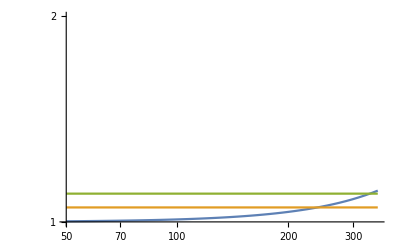

```mathematica
LogLogPlot[ {Abs[1/Q[[1,1]]],1.05, 1.1}, {ℓ, 50, 350}, PlotRange->{0, 2}]
```